#### Basic idea

(-10+5 (-10+2 k))^2+(10+5 (-10+2 k))^2

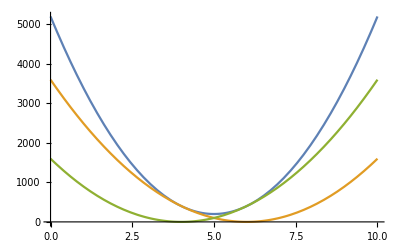

```mathematica
Np=10;a=5;
S=2*k-Np;
eq[x_]=(a*S-x)^2;
energy[k_]=(eq[10]+eq[-10])
Plot[{energy[k],eq[10],eq[-10]},{k,0,Np}]
```

#### Ah... the basic idea doesn’t even work. Adding quadratics just give more quadratics. DOH!

```mathematica
S1=2*k1-Np;
S2=2*k2-Np;
S3=2*k3-Np;
eq1[x_]=-S1-S2+S3+x;
eq2[x_]=-S1+S2-S3+x;
eq3[x_]=S1+S2+S3+x;
eq4[x_]=S1-S2-S3+x;
mpow=2;
energy[k1_,k2_,k3_]=(eq1[Np])^mpow;
```

```mathematica
Np=20;
targetlistcrit={};
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
For[k3=0,k3≤Np,k3=k3+1,
(*If[(k1+k2-Np<=k3)&&(-k1+k2+Np>=k3)&&(-k1-k2+Np<=k3)&&(k1-k2+Np>=k3)&&(Mod[k1+k2+k3+Np,2]==0),
targetlistcrit=Append[targetlistcrit,{k1,k2,k3}];
];*)
If[energy[k1,k2,k3]==0,targetlistcrit=Append[targetlistcrit,{k1,k2,k3}]];
];
];
];
p3=ListPointPlot3D[targetlistcrit,PlotStyle->Red,AxesLabel->{"k1","k2","k3"}]
```

-Graphics3D-